# Ma 4: Introduction to Mathematical Chaos

## 1. Introduction: What is chaos?

## The logistic map

### Cobweb diagrams for the logistic map

Kevin Reiss
“Cobweb Diagram of the Logistic Map”
http://demonstrations.wolfram.com/CobwebDiagramOfTheLogisticMap/
Wolfram Demonstrations Project
Published: May 20, 2021

### Bifurcation diagram

```mathematica
Manipulate[
 limits = Compile[{r},Map[{r,#}&, Union[Drop[ NestList[#*r(1-#)&,.234,pts],300]]]];
  bifurcation[r0_,r1_,n_] := Flatten[Table[limits[r], {r,r0,r1,(r1-r0)/n}], 1] ;
(*This formulation is modified from that given in Mathematica Navigator, 3rd edition by Heikki Ruskeepaa, Academic Press, 2009, page 941ff. This book is highly recommended for users of Mathematica 6 or 7.*)ListPlot[ bifurcation[beginr,If[endr<4,endr,4],pts], PlotStyle->AbsolutePointSize[0.1],
  AxesOrigin->{beginr,ylow}, PlotRange->{{beginr,If[endr<4,endr,4]},{ylow,yhigh}}, AxesLabel->{Style["r",18, Bold],Style["x_n",18,Bold]},PlotLabel->Style[Subscript[x, Style["n",Italic]+1]== r Subscript[x, Style["n",Italic]](1- Subscript[x, Style["n",Italic]]),18,Bold],ImageSize->{600,350},Frame->True,ImagePadding->25,
 Ticks->{Range[beginr,If[endr<4,(endr),4],((If[endr<4,(endr),4])-beginr)/5], Range[0,1,If[yhigh-ylow<.3,(yhigh-ylow)/10,0.1]]}],
Grid[{{Control[{{beginr,2.9,"beginning r"},1,3.9999,.01,ImageSize->Small,Appearance->"Labeled"}],Control[{{yhigh,1,"high end of y axis"},.01,1,.01,ImageSize->Small,Appearance->"Labeled"}]},
{Control[{{endr,4,"ending r"},2.9,4,.01,ImageSize->Small,Appearance->"Labeled"}],Control[{{ylow,0,"low end of y axis"},0,.99,.01,ImageSize->Small,Appearance->"Labeled"}]}},Alignment->Right],
{{pts,600,"number of points"},600,3000,300,Appearance->"Labeled"}, TrackedSymbols->True,SynchronousUpdating->False
]
```

### In the chaotic regime (e.g. at ), there are “dense orbits”: they come arbitrarily close to any point in [0,1]

The command NestList[f,x0,n] computes a list {x0,f(x0),f(f(x_0)),...,f^n(x_0)}

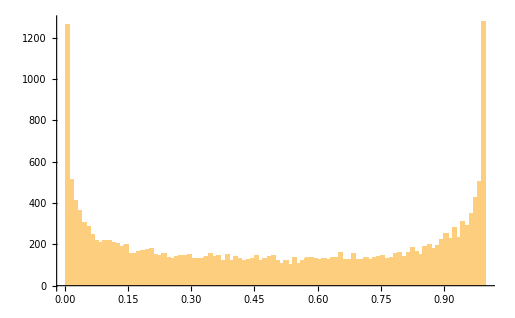

```mathematica
Logistic[r_]:=Function[x,r x (1-x)];
NestList[Logistic[4], 0.1, 2000];  
Histogram[NestList[Logistic[4], 0.1, 20000],100]
```

### In the chaotic regime (e.g. at ), the system exhibits sensitivity to initial conditions

For instance, we show here the value of   for  and .

```mathematica
L1:=NestList[Logistic[4], 0.00003, 100];
L2:=NestList[Logistic[4], 0.00006, 100];
L1[[100]]
L2[[100]]
```

0.170587

0.991606

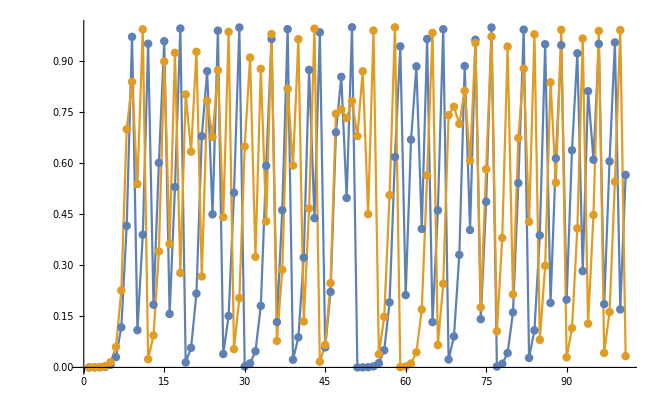

```mathematica
ListPlot[{L1,L2},Joined->True,Mesh->All,PlotRange->All]
```

### Evolution in time

#### Convergence to a fixed point for and .

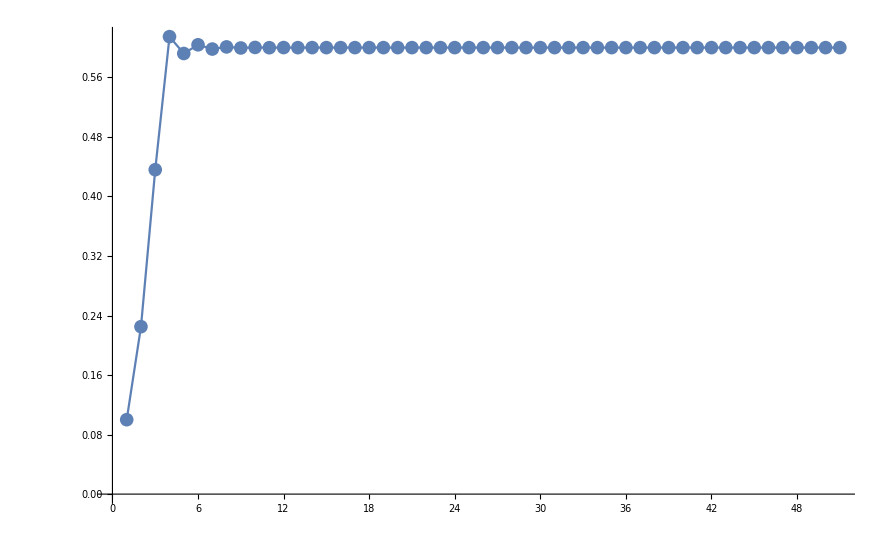

```mathematica
iterates:=NestList[Logistic[2.5], 0.1, 50]
ListPlot[iterates,Joined->True,Mesh->All,PlotRange->All]
```

#### Convergence to a 4-cycle point for and .

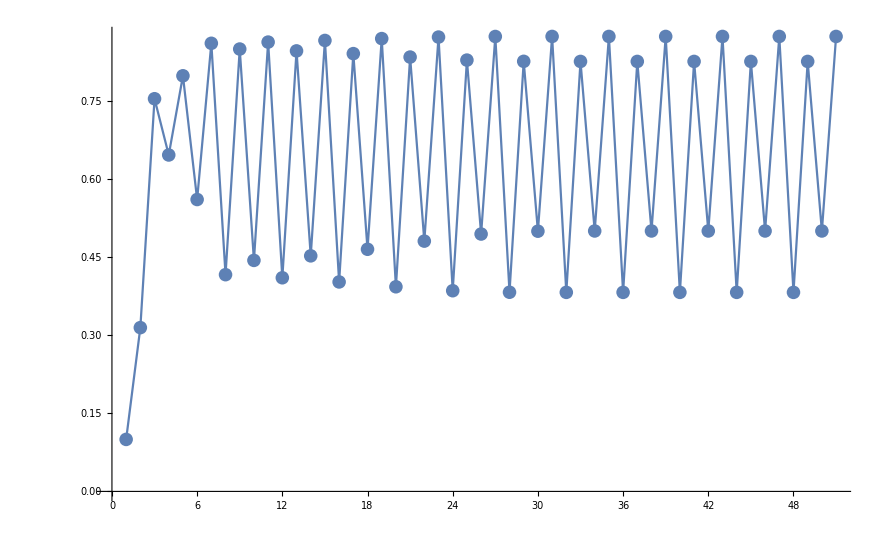

```mathematica
iterates:=NestList[Logistic[3.5], 0.1, 50]
ListPlot[iterates,Joined->True,Mesh->All,PlotRange->All]
```

#### Dense orbit for and .

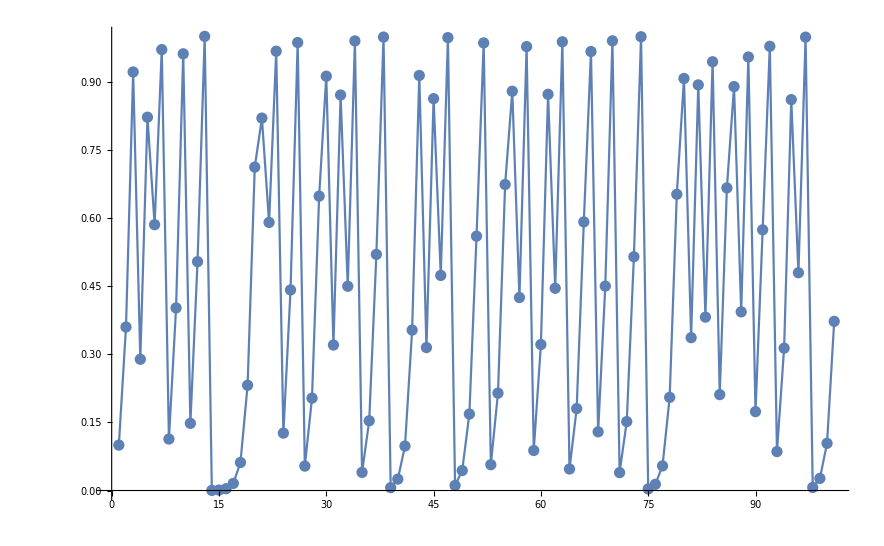

```mathematica
iterates:=NestList[Logistic[4], 0.1, 100]
ListPlot[iterates,Joined->True,Mesh->All,PlotRange->All]
```

## Julia sets

We consider here the iteration of complex functions  for different values of c. 
The regions in black converge to periodic solutions (including fixed points). 
The regions in color are those starting points that scape to infinity. 
The frontier between the two regions is a fractal and inside this fractal the dynamics under   are chaotic.

```mathematica
JuliaSetPlot[0]
```

-Graphics-

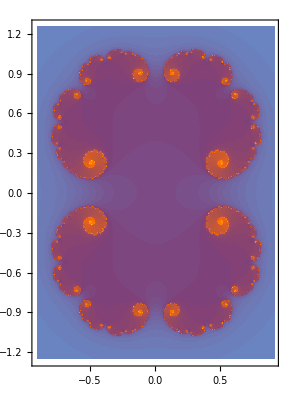

```mathematica
JuliaSetPlot[0.3]
```

### Douady’s rabbit:

The points in the black zone, asymptotically, have period 3.

```mathematica
JuliaSetPlot[-.122+.745*I]
```

-Graphics-

The points in the black zone, asymptotically, have period 11.

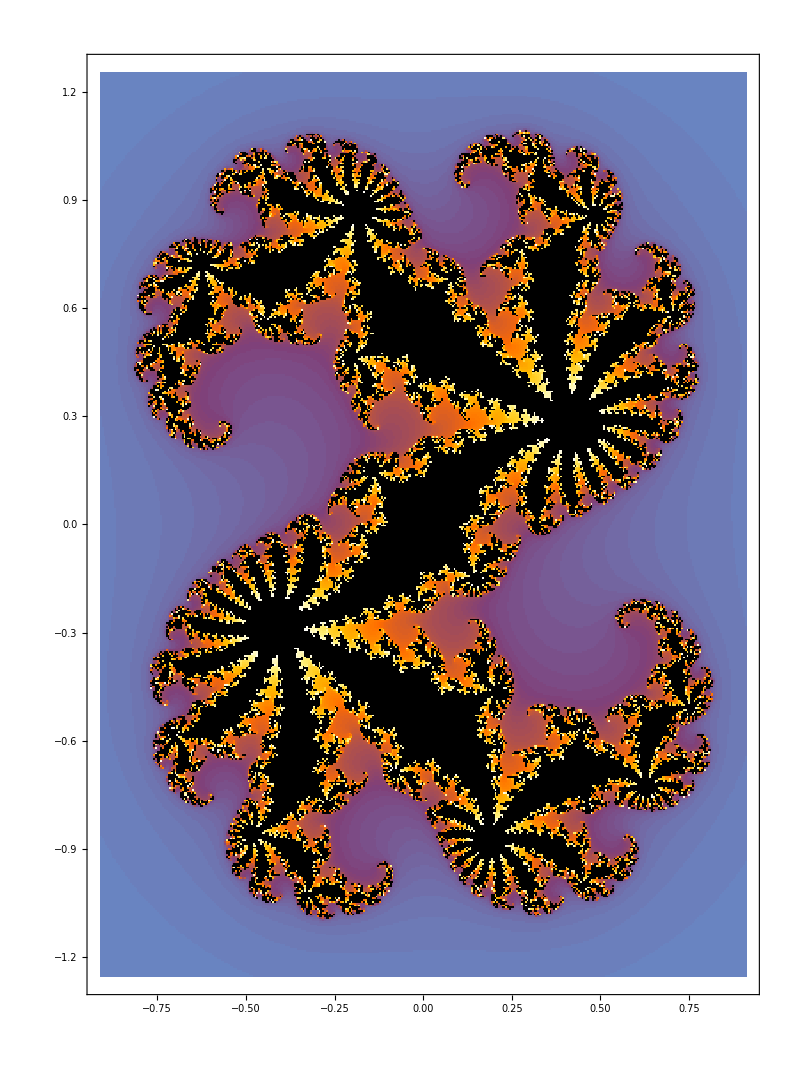

```mathematica
JuliaSetPlot[.32+.04*I]
```

### Dendrite:

```mathematica
JuliaSetPlot[I]
```

-Graphics-

## The Lorenz attractor

Consider the solutions of the system of differential equations, with unknowns :





where the parameters take the values =10, , .

```mathematica
euler[{x_,y_,z_}]:={x+.005 (-10(x-y)),y+.005 (-x z+28 x-y),z+.005 (x y-8*z/3)}

steps=10000;
init={0,1,0};

sol=NestList[euler,init,steps];

(*ListLinePlot[Transpose@sol]*)
p=Interpolation/@Transpose@sol;ParametricPlot3D[Through@p@x,{x,1,10000},PlotPoints->10000,ColorFunction->(Hue[#4]&)]
```

-Graphics3D-

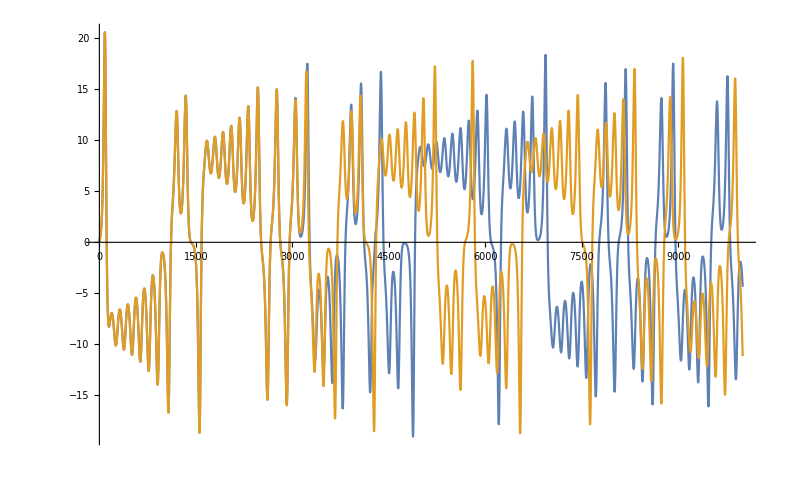

```mathematica
init1={0.001,1,0};
sol1=NestList[euler,init1,steps];
p1=Interpolation/@Transpose@sol1;
Show[Plot[{p[[1]][x], p1[[1]][x]},{x,1,10000}]]
```

Source: https://mathematica.stackexchange.com/questions/95897/plot-lorenz-system

## Three body problem -Graphics-

Source: Alligood, Sauer, Yorke: Chaos: An Introduction to Dynamical Systems, Springer, 1966.